```mathematica
Integrate[Exp[-(x+a)^2]/Sqrt[x],{x,0,Infinity}](*relation 1*)
```

(√a ⅇ^(-a^2/2) BesselK[1/4,a^2/2])/(√2)

```mathematica
Integrate[Exp[a x^2 +b x],{x,-Infinity,Infinity}](*relation 2*)
```

ConditionalExpression[(ⅇ^(-b^2/(4 a)) √π)/(√-a),Re[a]<0]

```mathematica
(*Calculate Eq-1.2:a=x Exp[-Pi I/4]/2, and When: x<0,(a^2)/2=Abs[x^2]Exp[-Pi I/2]Exp[2Pi I]/8; When x>0,(a^2)/2=Abs[x^2]Exp[-Pi I/2]/8*)
```

```mathematica
Bp[x_]:=If[x≤0,(√a ⅇ^(-a^2/2))/(√2)Exp[I/8 (Pi-2x^2)](Exp[- 2Pi I/4]BesselK[1/4,Exp[-I Pi/2]Abs[x^2]/8]-Pi I Sin[2Pi/4]Csc[Pi/4]BesselI[1/4,Exp[-I Pi/2]Abs[x^2]/8])/.{a->x Exp[3Pi I/4]/2},
(√a ⅇ^(-a^2/2))/(√2)Exp[I/8 (Pi-2x^2)](BesselK[1/4,Exp[-I Pi/2]Abs[x^2]/8])/.{a->x Exp[-Pi I/4]/2}]
```

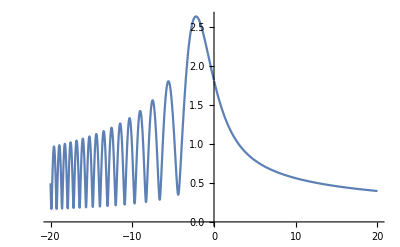

```mathematica
Plot[Bp[x]//Abs,{x,-20,20}]
```

```mathematica
(*calculate Eq1.2 by using its difinition*)
```

```mathematica
Pe[x_]:=NIntegrate[Exp[I(s^4 +x s^2)],{s,-Infinity,Infinity}]
```

```mathematica
list1=ParallelEvaluate[Array[Pe,551,{-20,20}]];
```

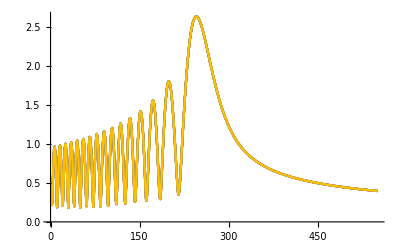

```mathematica
ListLinePlot[list1//Abs, PlotRange->All]
```

```mathematica
list2=ParallelEvaluate[Array[Bp,551,{-20,20}]]//N;
```

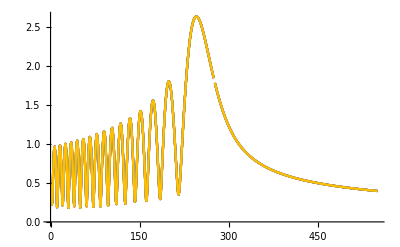

```mathematica
ListLinePlot[list2//Abs, PlotRange->All]
```

```mathematica
list0=Abs[list1]-Abs[list2];(*the difference of two methd is less than 10^-10, so our analytic continuation methd is right.*)
```

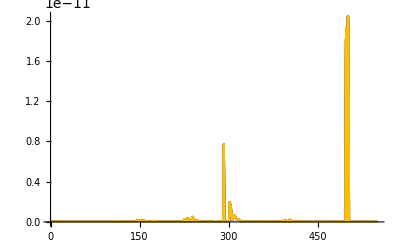

```mathematica
ListLinePlot[list0//Abs, PlotRange->All]
```

```mathematica
(*calculate Eq-1.9*)
```

```mathematica
x0=1.3 10^(-4);
```

```mathematica
w0=3 10^(-3);
```

```mathematica
k=2 Pi/(1064 10^(-9));
```

```mathematica
ze=2k x0 x0;
```

```mathematica
sa[z_]:=(1+2I z/k/w0/w0);
```

```mathematica
sa1[z_]:=1-z/ze/sa[z];(*sa1[z] represent the n in paper, and sqrt[sa1[z]] is the trasnversr scaling sqrt[n] in the Pearcey function*)
```

```mathematica
(*as see the complex angle of transverse scaling-sqrt[n] after ze=0.1996 have an abrupt change*)
```

```mathematica
sa1f[z_]:=Arg[sa1[z]];
```

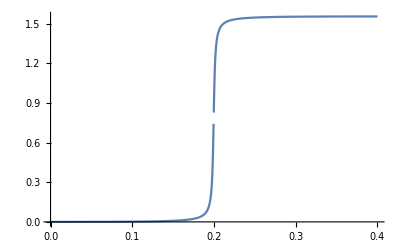

```mathematica
Plot[sa1f[z]/2,{z,0,0.4}]
```

```mathematica
(*sa1q[z] represent the amplitude of n in paper,)
```

```mathematica
sa1q[z_]:=Abs[sa1[z]];
```

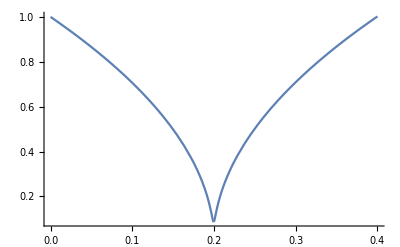

```mathematica
Plot[Sqrt[sa1q[z]],{z,0,0.4},PlotRange->All]
```

```mathematica
(*x(z)=x/x0/sa[z]/Sqrt[sa1[z]],(a^2)/2=(x(z)^2)/2*)
```

```mathematica
abm[z_]:=1/(Abs[sa1[z]])/Abs[sa[z]]/Abs[sa[z]]/8;(*the amplitude of (a^2)/2/(x/x0)^2*)
```

```mathematica
abf[z_]:=-Arg[sa1[z]]-2Arg[sa[z]]-Pi/2;(*the complex angle of (b^2)/8/a/(x/x0)^2*)
```

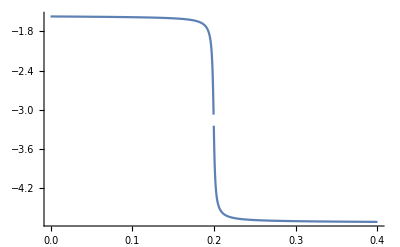

```mathematica
Plot[abf[z],{z,0,0.4},PlotRange->All]
```

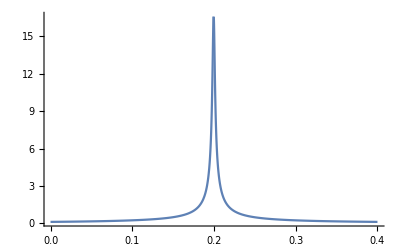

```mathematica
Plot[abm[z],{z,0,0.4},PlotRange->All]
```

```mathematica
m[z_]:=Quotient[abf[z],Pi];
```

```mathematica
Bpz[z_,x_]:=If[x≤0,(√a ⅇ^(-a^2/2))/(√2)Exp[I/8 (Pi-2(x /x0/sa[z]/Sqrt[sa1[z]])^2)]Sqrt[1/sa[z]]Exp[-(x^2)/w0/w0/sa[z]]Power[sa1[z],-1/4](Exp[- (m[z]+2)Pi I/4]BesselK[1/4,abm[z]Exp[(abf[z]I-m[z]Pi I)]Abs[(x/x0)^2]]-Pi I Sin[(m[z]+2)Pi/4]Csc[Pi/4]BesselI[1/4,abm[z]Exp[(abf[z]I-m[z]Pi I)]Abs[(x/x0)^2]])/.{a->x Exp[3Pi I/4]/x0/2/sa[z]/Sqrt[sa1[z]]},
(√a ⅇ^(-a^2/2))/(√2)Exp[I/8 (Pi-2(x /x0/sa[z]/Sqrt[sa1[z]])^2)]Sqrt[1/sa[z]]Exp[-(x^2)/w0/w0/sa[z]]Power[sa1[z],-1/4](Exp[- (m[z])Pi I/4]BesselK[1/4,abm[z]Exp[(abf[z]I-m[z]Pi I)]Abs[(x/x0)^2]]-Pi I Sin[(m[z])Pi/4]Csc[Pi/4]BesselI[1/4,abm[z]Exp[(abf[z]I-m[z]Pi I)]Abs[(x/x0)^2]])/.{a->x Exp[-Pi I/4]/x0/2/sa[z]/Sqrt[sa1[z]]}]
```

```mathematica
(*amplitude of Eq1.9 at 0m,0.1m,0.15m,ze,0.25m,0.3m*)
```

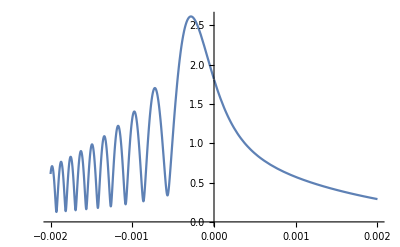

```mathematica
Plot[Abs[Bpz[0,x]],{x,-0.002,0.002}]
```

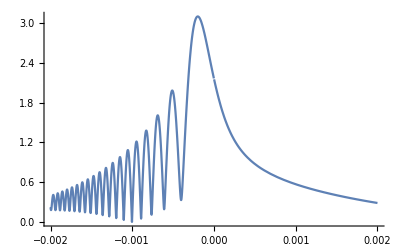

```mathematica
Plot[Abs[Bpz[0.1,x]],{x,-0.002,0.002},PlotRange->All]
```

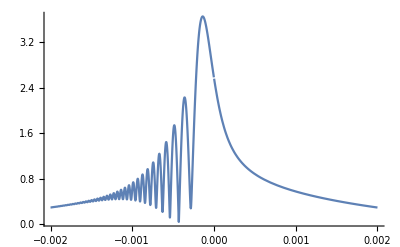

```mathematica
Plot[Abs[Bpz[0.15,x]],{x,-0.002,0.002},PlotRange->All]
```

General::munfl: Exp[-7876.79+59.5561 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

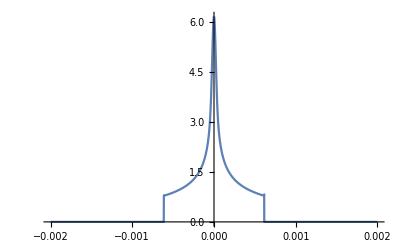

```mathematica
Plot[Abs[Bpz[ze,x]],{x,-0.002,0.002},PlotRange->All]
```

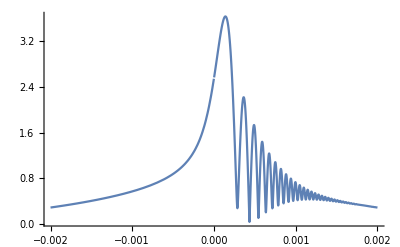

```mathematica
Plot[Abs[Bpz[0.25,x]],{x,-0.002,0.002},PlotRange->All]
```

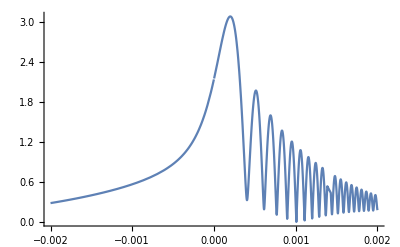

```mathematica
Plot[Abs[Bpz[0.3,x]],{x,-0.002,0.002},PlotRange->All]
```

```mathematica
(*intensity of Eq1.9 at 0m,0.1m,0.15m,ze,0.25m,0.3m* == cross line in fig1*)
```

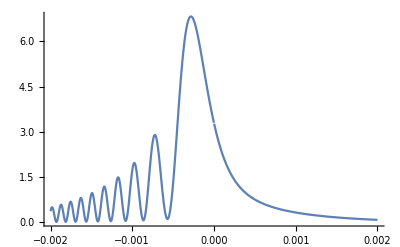

```mathematica
Plot[Abs[Bpz[0,x]]^2,{x,-0.002,0.002},PlotRange->All]
```

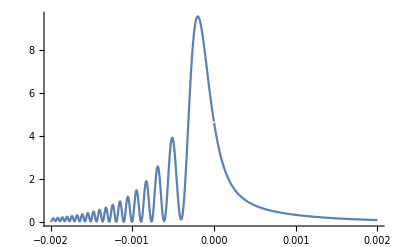

```mathematica
Plot[Abs[Bpz[0.1,x]]^2,{x,-0.002,0.002},PlotRange->All]
```

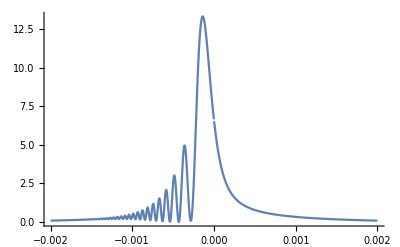

```mathematica
Plot[Abs[Bpz[0.15,x]]^2,{x,-0.002,0.002},PlotRange->All]
```

```mathematica
(*intensity of beams*)
```

General::munfl: Exp[-7876.79+59.5561 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

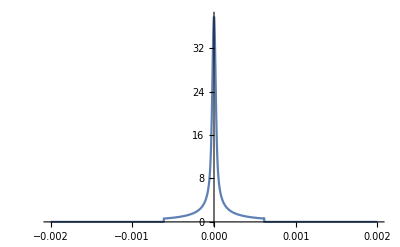

```mathematica
Plot[Abs[Bpz[ze,x]]^2,{x,-0.002,0.002},PlotRange->All]
```

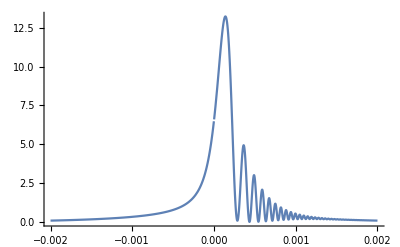

```mathematica
Plot[Abs[Bpz[0.25,x]]^2,{x,-0.002,0.002},PlotRange->All]
```

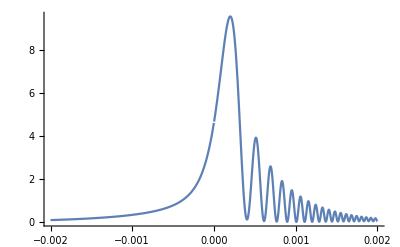

```mathematica
Plot[Abs[Bpz[0.3,x]]^2,{x,-0.002,0.002},PlotRange->All]
```